1 D forward and backward discrete Fourier transform

```mathematica
FFTw2t[a_,dt_]:=Fourier[a,FourierParameters->{-1,-1}]/dt
```

```mathematica
FFTt2w[a_,dt_]:=dt Fourier[a,FourierParameters->{1,1}]
```

The electron Green’s function

```mathematica
G[ω_,δ_,Δ_,vF_]:=-(ω+I δ)/(2vF √(Δ^2-(ω+I δ)^2))
```

Its imaginary part is the DOS:

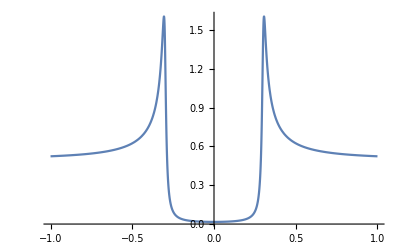

```mathematica
Plot[-Im[G[x,10^-2,0.3,1]],{x,-1,1},PlotRange->All]
```

Bose - Einstein distribution:

```mathematica
Bose[ω_,kT_]:=1/(Exp[ω/kT]-1)
```

The phonon factor:

-Graphics-

```mathematica
FF[λ_,ω0_,kT_,t_]:=-(λ^2/ω0)((Bose[ω0,kT]+1) (1-Exp[-ⅈ ω0 t])+Bose[ω0,kT] (1-Exp[ⅈ ω0 t]))
```

```mathematica
FFl=FF[1,20/2048,kT,#]&/@tl;
```

```mathematica
FFlw=FFTt2w[FFl,dt];
```

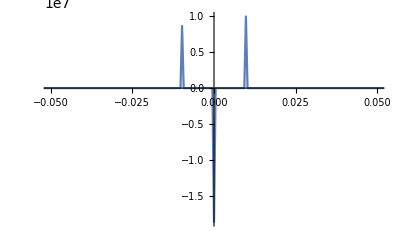

```mathematica
ListLinePlot[Sort[{ωl,FFlw//Re}//Transpose],PlotRange->{{-0.05,0.05},All},PlotStyle->PointSize[0.01]]
```

```mathematica
FFt[λ_,ω0s_,kT_,t_]:=Total[FF[λ,#,kT,t]&/@ω0s](ω0s[[2]]-ω0s[[1]])
```

```mathematica
EFF[λ_,ω0s_,kT_,t_]:=Exp[FFt[λ,ω0s,kT,t]]
```

Test to make sure FFT works: Less Green' s functon of phonons:

```mathematica
FFtless[λ_,ω0s_,kT_,t_]:=Total[((Bose[#,kT]+1) (Exp[ⅈ # t])+Bose[#,kT] (Exp[-ⅈ # t]))&/@ω0s](ω0s[[2]]-ω0s[[1]])
```

```mathematica
FFTts=FFtless[1,ω0s,kT,#]&/@tl;
```

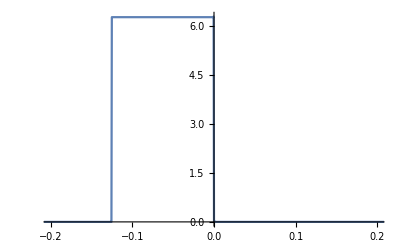

```mathematica
ListLinePlot[Sort[{ωl, FFTt2w[FFTts,dt]//Re}//Transpose],PlotRange->{{-0.2,0.2},All}]
```

## Caculations

### Parameters

Boltzmann constant (eV/K) and temperature (K):

```mathematica
kB=8.617330 10^-5;T=100;kT=kB T;
```

Small infinitesimal:

```mathematica
δ=10^-5;
```

Fermi velocity should not matter here, set to 1

```mathematica
vF=2.*^6;vF=1.0;
```

The CDW gap:

```mathematica
Δ=0.1;
```

Electron - phason coupling (all the other coefficients are also included here):

```mathematica
λ=0.75;
```

Energy points for electron spectrum:

```mathematica
NN=2048 2;
```

```mathematica
ωlh=2Range[NN]/NN;
```

```mathematica
ωl=Join[{0},ωlh[[;;-2]],-Reverse[ωlh]];
```

```mathematica
(ωl[[2]]-ωl[[1]])//N
```

0.000488281

Energy points for Phonon spectrum:

```mathematica
ω0s=ωl[[2;;257]];
```

```mathematica
ω0s=ωl[[2;;129]];
```

```mathematica
Max[ω0s]//N
```

0.0625

Time - step of FFT determined by the energy grids :

```mathematica
dt=(2 π)/((ωl⟦2⟧-ωl⟦1⟧) 2NN)
```

π/2

Time points:

```mathematica
tlh=Range[NN]dt;
```

```mathematica
tl=Join[{0},tlh[[;;-2]],-Reverse[tlh]];
```

### Single particle electron Green’s function:

```mathematica
Gl=G[#,δ,Δ,vF]&/@ωl;
```

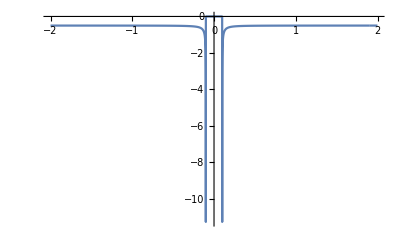

```mathematica
ListLinePlot[Sort[{ωl,Im[Gl]}//Transpose],PlotRange->All]
```

Its Fourier transform (ω->t):

```mathematica
Glt=FFTw2t[Gl,dt];
```

### The phonon part in time:

```mathematica
FFlt=EFF[λ,ω0s,kT,#]&/@tl;
```

The phonon part is frequency/energy:

```mathematica
FFlw=FFTt2w[FFlt,dt];
```

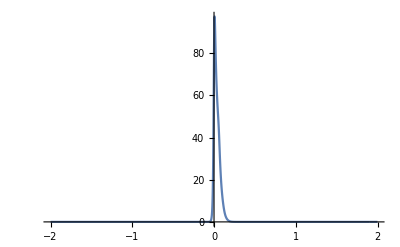

```mathematica
ListLinePlot[Sort[{ωl,FFlw//Re}//Transpose],PlotRange->{All,All}]
```

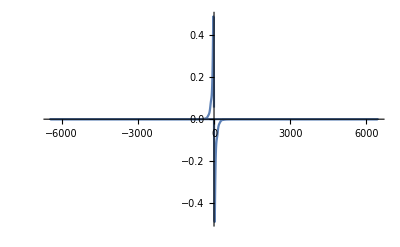

```mathematica
ListLinePlot[{tl,FFlt//Im}//Transpose,PlotRange->{All,All}]
```

### The spectrum including electron-phason coupling:

Multiplication of the two and inverse Fourier transform:

```mathematica
Glm=FFTt2w[FFlt Glt,dt];
```

```mathematica
Aph=ListLinePlot[Sort[Transpose[{ωl,-Im[Glm]}]],PlotRange->{{-0.5,0.5},All},Frame->True,FrameLabel->{"Energy (eV)","DOS"},PlotLabel->"T=100 K,λ=0.75"];
```

The single particle spectrum:

```mathematica
Glm0=FFTt2w[Glt ,dt];
```

```mathematica
Aph1=Aph;
```

```mathematica
Aph100=Aph;
```

```mathematica
A0=ListLinePlot[Sort[Transpose[{ωl,-Im[Glm0]}]],PlotRange->{{-0.5,0.5},All},Frame->True,FrameLabel->{"Energy (eV)","DOS"},PlotLabel->"λ=0"];
```

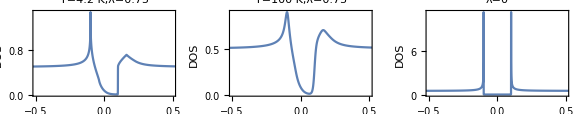

```mathematica
plt=GraphicsGrid[{{Aph1, Aph100, A0}}, ImageSize -> Large]
```

```mathematica
Export["par2.png",plt]
```

par2.png